```mathematica
fnew[n_Integer]:=n-fnew[fnew[n-2]]
a=1;
Clear[a];
fnew[1]=a;
fnew[2]=b;
```

```mathematica
Table[fnew[i], {i, 1, 20, 2}]//Column
```

a
3-fnew[a]
5-fnew[3-fnew[a]]
7-fnew[5-fnew[3-fnew[a]]]
9-fnew[7-fnew[5-fnew[3-fnew[a]]]]
11-fnew[9-fnew[7-fnew[5-fnew[3-fnew[a]]]]]
13-fnew[11-fnew[9-fnew[7-fnew[5-fnew[3-fnew[a]]]]]]
15-fnew[13-fnew[11-fnew[9-fnew[7-fnew[5-fnew[3-fnew[a]]]]]]]
17-fnew[15-fnew[13-fnew[11-fnew[9-fnew[7-fnew[5-fnew[3-fnew[a]]]]]]]]
19-fnew[17-fnew[15-fnew[13-fnew[11-fnew[9-fnew[7-fnew[5-fnew[3-fnew[a]]]]]]]]]

Every odd value depends on a, every even value depends on b

Odds:

```mathematica
Table[f[i], {i, 1, 20, 2}]//Column
```

a
3-f[a]
5-f[3-f[a]]
7-f[5-f[3-f[a]]]
9-f[7-f[5-f[3-f[a]]]]
11-f[9-f[7-f[5-f[3-f[a]]]]]
13-f[11-f[9-f[7-f[5-f[3-f[a]]]]]]
15-f[13-f[11-f[9-f[7-f[5-f[3-f[a]]]]]]]
17-f[15-f[13-f[11-f[9-f[7-f[5-f[3-f[a]]]]]]]]
19-f[17-f[15-f[13-f[11-f[9-f[7-f[5-f[3-f[a]]]]]]]]]

So g[x] = 2x+1 - g[x-1]

```mathematica
g[n_]:=2n-1-g[n-1]
g[1]=a;
```

```mathematica
goriginal[n_]:=2n-1-goriginal[n-1]
goriginal[1]=1;
```

```mathematica
goriginal[8]
```

8

Evens:

```mathematica
Table[f[i], {i, 2, 20, 2}]//Column
```

b
4-f[b]
6-f[4-f[b]]
8-f[6-f[4-f[b]]]
10-f[8-f[6-f[4-f[b]]]]
12-f[10-f[8-f[6-f[4-f[b]]]]]
14-f[12-f[10-f[8-f[6-f[4-f[b]]]]]]
16-f[14-f[12-f[10-f[8-f[6-f[4-f[b]]]]]]]
18-f[16-f[14-f[12-f[10-f[8-f[6-f[4-f[b]]]]]]]]
20-f[18-f[16-f[14-f[12-f[10-f[8-f[6-f[4-f[b]]]]]]]]]

```mathematica
foriginal[n_]:=foriginal[n]=n-foriginal[foriginal[n-2]]
foriginal[1]=1;
foriginal[2]=1;
```

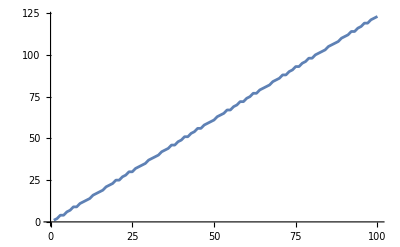

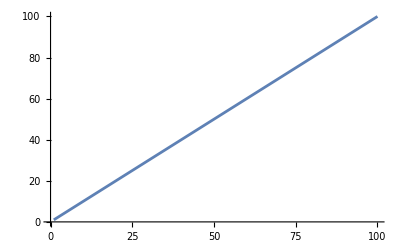

```mathematica
Table[foriginal[i], {i, 1, 200, 2}]//ListLinePlot
Table[With[{a=1},goriginal[i]], {i, 1, 100}]//ListLinePlot
```

```mathematica
Table[foriginal[i], {i, 100}]
```

{1,1,2,3,4,4,4,5,6,6,7,8,9,9,9,10,11,12,12,12,13,14,14,15,16,17,17,17,18,19,19,20,21,22,22,22,23,24,25,25,25,26,27,27,28,29,30,30,30,31,32,33,33,33,34,35,35,36,37,38,38,38,39,40,40,41,42,43,43,43,44,45,46,46,46,47,48,48,49,50,51,51,51,52,53,53,54,55,56,56,56,57,58,59,59,59,60,61,61,62}